## multilevel Cs Single excited state F4. Ground states F3, F4

(pol absorbed | initial state | final state | <n>
1 | {3,3} | {4,4} | 1.27)

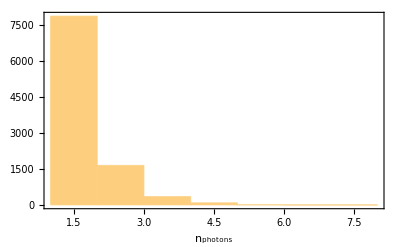

(pol emitted | <n>
-1 | 0.
0 | 1.
1 | 0.27)

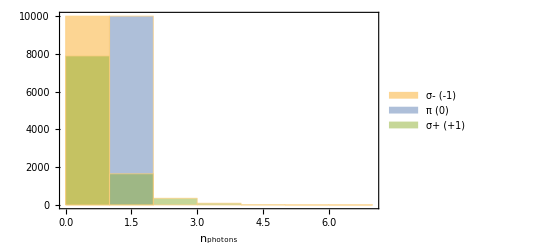

(pol | <n_total>
-1 | 0.
0 | 1.
1 | 1.54)

```mathematica
Clear["Global`*"]
Needs["PlotLegends`"]
(*--------------------------parameters----------------------------------*)
{F0,mF0}={3,3}; {3,0};(*initial state; pick from an initial distribution*)
{Ffin,mFfin}={4,4}; {4,0};(*final state to pump to*)
pol=1;0; (*pumping pol, -1,0,1 = sigma-,pi,sigma+*)

MHz = 10^6;
kHz=10^3;
us = 10^-6;
ms=10^-3;

Fe=4;
Fg1=4;(*bigger*)
Fg2=3;(*smaller*)
nSim=10000;
nMax=100;(*stop simulation automatically if it goes over nMax photons*)

(*Fg,σp,π0,σm,POL*)
(*list params in order of DECREASING F!!! (for later definition of iMon)*)
params1=
{Fg1, 
{7/120,49/480,21/160,7/48,7/48,21/160,49/480,7/120},
{-7/30,-21/160,-7/120,-7/480,0,7/480,7/120,21/160,7/30},
-{7/120,49/480,21/160,7/48,7/48,21/160,49/480,7/120}
};

params2=
{Fg2, 
{7/72,7/96,5/96,5/144,1/48,1/96,1/288},
{7/288,1/24,5/96,1/18,5/96,1/24,7/288},
Reverse[ {7/72,7/96,5/96,5/144,1/48,1/96,1/288}]
};

(*--------------------------Functions to Pad with Zero rows or columns either at first or last position.----------------------------------*)
AddRows[list0_,pos0_,n0_]:=
Module[{list=list0,pos = pos0,n=n0},
(*pos=-1, add to end, anything else-->add to beginning*)
If[pos==-1,
list=Join[list,ConstantArray[0,{n,Length[list]}]],
list=Join[ConstantArray[0,{n,Length[list]}],list]
]
];

AddColumns[list0_,pos0_,n0_]:=
Module[{list=list0,pos = pos0,n=n0},
(*pos=-1, add to end, anything else-->add to beginning*)
If[pos==-1,
list=PadRight[#,Length[#]+n]&/@list,
list=PadLeft[#,Length[#]+n]&/@list
]
];
(*--------------------------function to generate big ass matrix.----------------------------------*)
GenerateDecay[Fe0_,Fg0_,σp0_,π00_,σm0_]:=
Block[{Fe=Fe0,Fg=Fg0,σp=σp0,π0=π00,σm=σm0},

Mπ0=DiagonalMatrix[π0];
Mσm=DiagonalMatrix[σm];
Mσp=DiagonalMatrix[σp];


Switch[Fe-Fg ,
-1,
Mσp=AddRows[Mσp,-1,2];
Mπ0=AddRows[Mπ0,-1,1];
Mπ0=AddRows[Mπ0,1,1];
Mσm=AddRows[Mσm,1,2];,

0,
Mσp=AddRows[Mσp,-1,1];
Mσp=AddColumns[Mσp,1,1];
Mσm=AddRows[Mσm,1,1];
Mσm=AddColumns[Mσm,-1,1];,

1,
Mσp=AddColumns[Mσp,1,2];
Mπ0=AddColumns[Mπ0,-1,1];
Mπ0=AddColumns[Mπ0,1,1];
Mσm=AddColumns[Mσm,-1,2];

];

(*generate block matrix for decays from E-->G*)
Mσp+Mπ0+Mσm
];

(*--------------------------------------------------generate big ass matrix-----------------------------------------------------------*)
b=Reap[Do[
{Fg,σp,π0,σm}=params;
(*generate block matrix for ALL decays out of E-->G*)
Sow[{Fg,GenerateDecay[Fe,Fg,σp,π0,σm]}];
,{params,{params1,params2}}]
][[2,1]];

(*sort from largest Fg to smallest Fg*)
b=Sort[b,#1[[1]]>#2[[1]]&];
(*concatenate Gnd state matrices together, vertically.*)
b=Join[Flatten[b[[;;,2]],1]];
(*-use ABS, all +ve, because decays go INTO gnd state, not out of it.*)
b=Abs[b]; 

(*normalize columns to Γ*)
b=#/Total[#]&/@Transpose[b];
(*partial sum L->R across each row*)
b=Table[Total[b[[i]][[;;#]]]&/@Range[Length[b[[1]]]],{i,Length[b]}];

(*----------------------------------------------monte carlo-----------------------------------------------*)
indexGfin=If[Ffin==Fg1,
(Fg1+1)+mFfin,
(2 Fg1+1)+(Fg2+1)+mFfin
];

ns=Reap[
Do[
mFk=mF0;
n=0; (*number of photons absorbed*)
emits={0,0,0}; (*number of photons emitted; σ-, π, σ+*)
indexG=If[F0==Fg1,
(Fg1+1)+mFk,
(2 Fg1+1)+(Fg2+1)+mFk
];

While[(indexG!=indexGfin)&&n<nMax,
mFk=mFk+pol;(*increment mF by amount according to polarization of OP*)
indexE=mFk+(Fe+1); (*convert to index*)
mFE=mFk;
(*Print["m_F="<>ToString[mFE]<>" in excited state"];*)
n=n+1; (*increment photon counter*)
probdecay=RandomReal[]; (*pick a random number from 0-1*)
bool=Boole[probdecay>#&/@b[[indexE]]];(*which gnd state it falls to*)
indexG=Total[bool]+1;(*index for the gnd state*)
mFk=If[indexG>(2 Fg1+1),
(*F3*)
indexG-(2 Fg1+1)-(Fg2+1),
(*F4*)
indexG-(Fg1+1)];
mFG=mFk;
emit=Switch[mFE-mFG,
+1,"σ+",
-1,"σ-",
0,"π"
];
emits[[mFE-mFG+2]]=emits[[mFE-mFG+2]]+1;
(*Print["m_F="<>ToString[mFG]<>" in gnd state"];
Print["emitted "<>emit];*)
];
(*
Print[ToString[n]];
Print["done"];
*)
Sow[{n,emits}],
{i,nSim}]
][[2,1]];

{{"pol absorbed","initial state","final state","<n>"},{pol,{F0,mF0},{Ffin,mFfin},Round[ Mean[ns[[;;,1]]],.01]}}//MatrixForm
Histogram[ns[[;;,1]],Axes->False,Frame->True,FrameLabel->{"n_photons"},LabelStyle->Medium]
Join[{{"pol emitted","<n>"}},{#,Round[ Mean[ns[[;;,2]][[;;,#+2]]],.01]}&/@{-1,0,1}]//MatrixForm
Histogram[ns[[;;,2]][[;;,#+2]]&/@{-1,0,1},Axes->False,Frame->True,FrameLabel->{"n_photons"},LabelStyle->Medium,ChartLegends->{"σ- (-1)","π (0)","σ+ (+1)"}]

(*total number of photon kicks in each polarization*)
totalns=Mean[ns[[;;,2]][[;;,#]]]&/@{1,2,3};
totalns[[pol+2]]= Mean[
ns[[;;,1]]+ns[[;;,2]][[;;,pol+2]]
];
totalns=Thread[{{-1,0,1},Round[totalns,.01]}];
Join[{{"pol","<n_total>"}},totalns]//MatrixForm
```